```mathematica
Np=5;
Id=Table[KroneckerDelta[k1,k1p],{k1,0,Np},{k1p,0,Np}];
Sx=Table[KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sy=Table[-I*KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+I*KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sz=Table[KroneckerDelta[k1,k1p]*(2*k1-Np),{k1,0,Np},{k1p,0,Np}];
ghzstate=ArrayReshape[Table[KroneckerDelta[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];
ghzstate=N[Normalize[ghzstate]];
psi0[k1_,k2_,k3_]=(1/Sqrt[2]^(3*Np))*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]];
psi1[k1_,k2_,k3_]=(1/Sqrt[Np+1])*KroneckerDelta[k1,k2]*(1/Sqrt[2]^(Np))*Sqrt[Binomial[Np,k3]];
Urotzx1=MatrixExp[I*Sy*Pi/4];
Urotzx=KroneckerProduct[Urotzx1,Urotzx1,Urotzx1];
Urotxz=ConjugateTranspose[Urotzx];
Idbig=KroneckerProduct[Id,Id,Id];
psivec0=ArrayReshape[Table[psi1[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];Hamz=2*(KroneckerProduct[Sz.Sz,Id,Id]+KroneckerProduct[Id,Sz.Sz,Id]+KroneckerProduct[Id,Id,Sz.Sz])-2*(KroneckerProduct[Sz,Sz,Id]+KroneckerProduct[Sz,Id,Sz]+KroneckerProduct[Id,Sz,Sz]);
Hamx1=MatrixPower[(-KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig),2];
Hamx2=(-KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamx3=(KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamx4=(KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
```

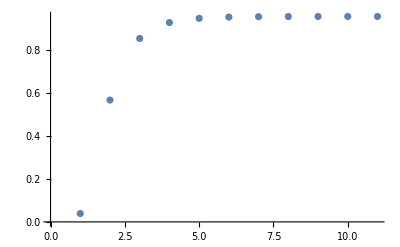

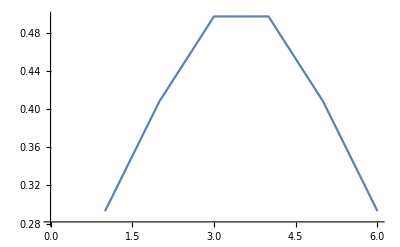

final psi={0.293037,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.408375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.497352,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.497352,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.408375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.293037}

ghz={0.408248,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.408248,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.408248,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.408248,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.408248,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.408248}

0.958024

```mathematica
t=10.0;
nrounds=10;
projmatx[1]=Urotzx.MatrixExp[-Hamx1*t].Urotxz;
projmatx[2]=Urotzx.MatrixExp[-Hamx2*t].Urotxz;
projmatx[3]=Urotzx.MatrixExp[-Hamx3*t].Urotxz;
projmatx[4]=Urotzx.MatrixExp[-Hamx4*t].Urotxz;
projmatz=MatrixExp[-Hamz*t];
psi=Normalize[ArrayReshape[Table[psi0[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]]];
fidlist={Abs[Conjugate[ghzstate].psi]^2};
For[n=1,n≤nrounds,n=n+1,
psi=Normalize[projmatz.projmatx[Mod[n,4]+1].psi];
fidlist=Append[fidlist,Abs[Conjugate[ghzstate].psi]^2];
];
psielem=Table[ArrayReshape[psi,{Np+1,Np+1,Np+1}][[k,k,k]],{k,1,Np+1}];
p1=ListPlot[fidlist];
Print[p1];
p2=ListPlot[psielem,Joined->True];
Print[p2];
Print["final psi=",Chop[psi]];
Print["ghz=",ghzstate];
Print[Last[fidlist]];
```

```mathematica
psielem
```

{0.293037,0.408375,0.497352,0.497352,0.408375,0.293037}

```mathematica
psicomp=Normalize[Table[N[Binomial[Np,k]^(0.25)],{k,0,Np}]]
```

{0.279545,0.418017,0.497108,0.497108,0.418017,0.279545}

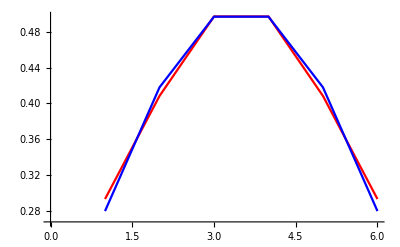

```mathematica
ListPlot[{psielem,psicomp},Joined->True,PlotStyle->{Red,Blue}]
```

#### This doesn’t help

```mathematica
sol=Eigensystem[projmatz.projmatx[1]]
```

{{0.405175,0.138607,0.119425,3.00315×10^-17,-1.48004×10^-18,-6.8935×10^-31,3.27984×10^-32,-2.93273×10^-32,2.56702×10^-32,2.21652×10^-32,2.06377×10^-32,-1.16104×10^-32,8.40491×10^-33,7.5951×10^-33,7.5951×10^-33,-5.30324×10^-33,184,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1}}
 |  |  |  |

```mathematica
sol[[1]]
```

{0.405175,0.138607,0.119425,3.00315×10^-17,-1.48004×10^-18,-6.8935×10^-31,3.27984×10^-32,-2.93273×10^-32,2.56702×10^-32,2.21652×10^-32,2.06377×10^-32,-1.16104×10^-32,8.40491×10^-33,7.5951×10^-33,7.5951×10^-33,-5.30324×10^-33,4.26672×10^-33,4.26672×10^-33,-3.86413×10^-33,-3.86413×10^-33,-3.75531×10^-33,3.70949×10^-33,3.48072×10^-33,3.48072×10^-33,2.84716×10^-33,-2.33995×10^-33,2.30356×10^-33,2.30356×10^-33,-2.00263×10^-33,-2.00263×10^-33,1.47699×10^-33,-7.42075×10^-34,-7.42075×10^-34,4.86632×10^-34,4.86632×10^-34,3.92804×10^-34,-1.93691×10^-34,-1.93691×10^-34,-1.36167×10^-34,-1.36167×10^-34,-9.67894×10^-35,6.58823×10^-35,5.73637×10^-35,5.73637×10^-35,2.34566×10^-35,9.46649×10^-36,9.46649×10^-36,-4.72247×10^-36,-4.72247×10^-36,5.20711×10^-50,-4.20721×10^-50,-4.20721×10^-50,4.13351×10^-59,4.13351×10^-59,-4.1335×10^-59,-4.1335×10^-59,-1.50508×10^-61,-1.50508×10^-61,-1.45945×10^-61,6.55976×10^-62,6.55976×10^-62,-5.69713×10^-62,-5.69713×10^-62,4.23334×10^-62,4.23334×10^-62,-3.54686×10^-62,-3.54686×10^-62,-3.30008×10^-62,-3.30008×10^-62,2.57608×10^-62,2.57608×10^-62,-2.51005×10^-62,-2.51005×10^-62,1.14284×10^-62,5.63993×10^-63,-5.49454×10^-63,-5.49454×10^-63,-3.45159×10^-63,2.33582×10^-63,2.33582×10^-63,-2.1348×10^-63,-2.1348×10^-63,1.05016×10^-63,-2.63845×10^-64,-8.37651×10^-65,-6.843×10^-65,5.47835×10^-65,-3.09792×10^-65,-1.91576×10^-65,-1.86017×10^-65,-1.86017×10^-65,1.83772×10^-65,1.83772×10^-65,1.70257×10^-65,-1.07923×10^-65,-1.07923×10^-65,8.40323×10^-66,8.40323×10^-66,-4.12867×10^-66,-2.64202×10^-66,-2.64202×10^-66,-2.56332×10^-66,-2.56332×10^-66,2.2672×10^-66,3.92528×10^-67,3.92528×10^-67,-7.76171×10^-83,1.11562×10^-94,-1.27781×10^-95,9.46338×10^-96,-4.7988×10^-96,-4.01556×10^-96,-4.01556×10^-96,-3.25016×10^-96,-3.16051×10^-96,2.86179×10^-96,2.86179×10^-96,2.63263×10^-96,2.63263×10^-96,2.3122×10^-96,1.75166×10^-96,1.75166×10^-96,-1.31475×10^-96,-1.31475×10^-96,1.24096×10^-96,1.24096×10^-96,-1.16364×10^-96,-1.16364×10^-96,-6.32616×10^-97,5.75416×10^-97,5.75416×10^-97,-4.73036×10^-97,-4.73036×10^-97,-3.75155×10^-99,-1.70441×10^-102,3.64133×10^-113,-2.08834×10^-113,-6.7716×10^-116,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Chop[sol[[2]][[1]]]
```

{-0.293057,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.408376,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.497339,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.497339,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.408376,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.293057}

```mathematica
Chop[psi]
```

{0.293037,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.408375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.497352,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.497352,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.408375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.293037}